```mathematica
Plot3D[Cosh[x] Cos[y],{x,-2,2},{y,-Pi,Pi},PlotRange->All,AxesLabel->{"x","y","Re[cosh(z)]"},ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
Plot3D[Sinh[x] Sin[y],{x,-2,2},{y,-Pi,Pi},PlotRange->All,AxesLabel->{"x","y","Im[cosh(z)]"},ColorFunction->"Rainbow"]
```

-Graphics3D-

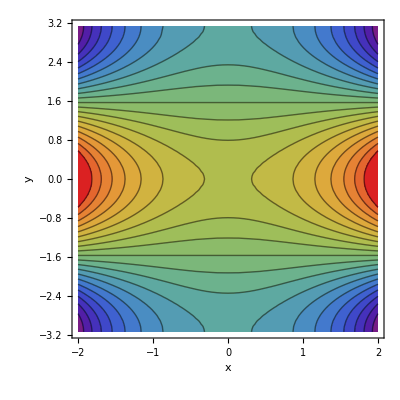

```mathematica
ContourPlot[Cosh[x] Cos[y],{x,-2,2},{y,-Pi,Pi},Contours->20,ColorFunction->"Rainbow",AxesLabel->{"x","y"}]
```

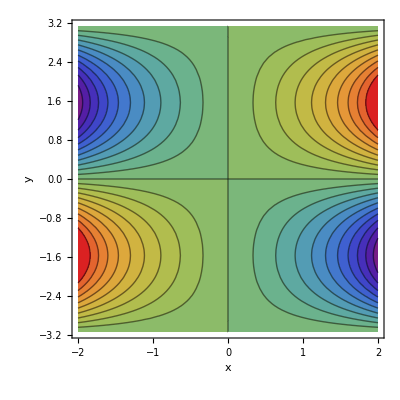

```mathematica
ContourPlot[Sinh[x] Sin[y],{x,-2,2},{y,-Pi,Pi},Contours->20,ColorFunction->"Rainbow",AxesLabel->{"x","y"}]
```

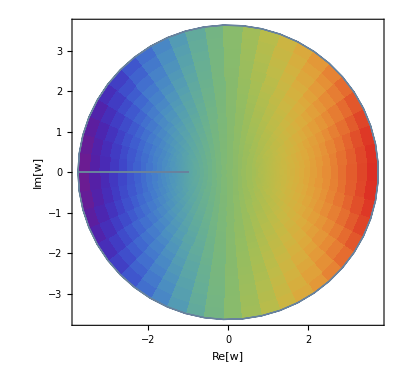

```mathematica
ParametricPlot[{Cosh[x] Cos[y],Sinh[x] Sin[y]},{x,-2,2},{y,-Pi,Pi},PlotPoints->50,AxesLabel->{"Re[w]","Im[w]"},ColorFunction->"Rainbow"]
```

```mathematica
Manipulate[ParametricPlot[{Cosh[x] Cos[y],Sinh[x] Sin[y]},{x,-2,2},{y,-a,a},PlotPoints->50,AxesLabel->{"Re[w]","Im[w]"}],{a,0.1,Pi}]
```